# DM DM -> h2 h2

```mathematica
Quit;
```

```mathematica
ClearAll["Global`*"];
$FeynArtsPath=SetDirectory["~/Work/FeynArts-3.9"]
<<FeynArts`
SetDirectory[$FeynArtsPath<>""]
$FormCalcPath=SetDirectory["~/Work/FormCalc-8.3"]
<<FormCalc`
SetDirectory[$FormCalcPath<>""]
```

/home/anferivera/Work/FeynArts-3.9

FeynArts 3.9 (8 Jul 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

/home/anferivera/Work/FeynArts-3.9

/home/anferivera/Work/FormCalc-8.3

FormCalc 8.3

by Thomas Hahn

last revised 14 Nov 13

/home/anferivera/Work/FormCalc-8.3

## Load the model, choose the topology and the diagram

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

loading generic model file /home/anferivera/Work/FeynArts-3.9/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/anferivera/Work/FeynArts-3.9/Models/SDdiracDMvsEWSB.mod

> 54 particles (incl. antiparticles) in 19 classes

> $CounterTerms are ON

> 108 vertices

classes model {SDdiracDMvsEWSB} initialized

Excluding 0 Generic, 0 Classes, and 3 Particles fields

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

Restoring 0 Generic, 0 Classes, and 3 Particles fields

in total: 3 Particles insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

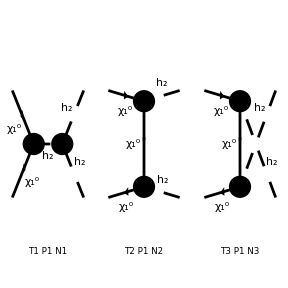

FeynArtsGraphics[{ComposedChar[\chi,1,0],ComposedChar[\chi,1,0]}→{ComposedChar[h,2],ComposedChar[h,2]}][([T1 P1 N1] | [T2 P1 N2] | [T3 P1 N3]
Null | Null | Null)]

```mathematica
ClearProcess[];
n22=CreateTopologies[0,2->2]

d22=InsertFields[n22,{F[6,{1}],-F[6,{1}]}->{S[1,{2}],S[1,{2}]}, InsertionLevel->{Particles},Model->"SDdiracDMvsEWSB",GenericModel->"Lorentz",ExcludeParticles->{S[1,{1}],F[6,{2}] }];
(*d22=InsertFields[n22,{F[6,{1}],-F[6,{1}]}->{V[3],-V[3]}, InsertionLevel->{Particles},Model->"SDdiracDMvsEWSB",GenericModel->"Lorentz"];*)
Paint[d22,ColumnsXRows->{3,2}]
```

> Top. 1: 1 diagram

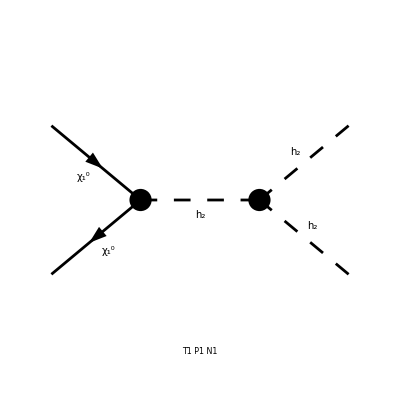

FeynArtsGraphics[{ComposedChar[\chi,1,0],ComposedChar[\chi,1,0]}→{ComposedChar[h,2],ComposedChar[h,2]}][([T1 P1 N1] | Null | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[d22[[{1}]]]
```

## Amplitude

```mathematica
amp=CreateFeynAmp[d22[[{1}]]]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

FeynAmpList[Process→{{F[6,{1}],p1,MassFxv[1],{}},{-F[6,{1}],p2,MassFxv[1],{}}}→{{S[1,{2}],k1,Masshh[2],{}},{S[1,{2}],k2,Masshh[2],{}}},Model→{SDdiracDMvsEWSB},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{-F[6,{2}],F[6,{2}],S[1,{1}]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[],-3 ⅈ v̄[p2,MassFxv[1]].(-(ⅈ XU[1,2]^* om_- (YRD XV[1,1]^* ZH[2,1]+YRC XV[1,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[1,1] ZH[2,1]+YRC XV[1,2] ZH[2,2]))/(√2)).u[p1,MassFxv[1]] 1/((k1+k2)^2-Masshh[2]^2) (Lam vvSM ZH[2,1]^3+LSP vS ZH[2,2]^3)]]

```mathematica
amp2 = amp/.{ ZH[x_,y_]->KroneckerDelta[x,y]}
```

```mathematica
amp2 = amp/.{ XU[x_,y_]->KroneckerDelta[x,y], XV[x_,y_]->KroneckerDelta[x,y],MassFxv[1]->100,MassFxv[2]->100,Masshh[1]->125,Masshh[2]->225, LSP->0.1, vS->200, YRD->0.2,vvSM->246, Lam->0.3,LSP->0.1}
```

FeynAmpList[Process→{{F[6,{1}],p1,100,{}},{-F[6,{1}],p2,100,{}}}→{{S[1,{2}],k1,225,{}},{S[1,{2}],k2,225,{}}},Model→{SDdiracDMvsEWSB},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{-F[6,{2}],F[6,{2}],S[1,{1}]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[],-3 ⅈ v̄[p2,100].0..u[p1,100] 1/(-50625+(k1+k2)^2) (73.8 ZH[2,1]^3+200 LSP ZH[2,2]^3)]]

```mathematica
resultamp = CalcFeynAmp[amp2]
```

preparing FORM code in /home/anferivera/Work/FormCalc-8.3/fc-amp-9.frm

running FORM...

ReadForm::formerror: \!\(\*RowBox[{"\"Illegal charact\\nIllegal positio\\nUndeclared vari\""}]\)

$Aborted

```mathematica
resultamp = CalcFeynAmp[amp,FermionChains->VA,FermionOrder->None,  Invariants->True]
```

preparing FORM code in /home/anferivera/Work/FormCalc-8.3/fc-amp-9.frm

running FORM...

ReadForm::formerror: \!\(\*RowBox[{"\"Undeclared vari\""}]\)

$Aborted

```mathematica
Den[x_,y_]:=1/(x-y)
expr1=ComplexExpand[Plus@@resultamp//.Subexpr[]//.Abbr[]]/.Alfa->e^2/(4Pi)//.{ME->Me,ME2->Me^2}
```

0

This is the equation 9.33 (A first book in QFT, LAHIRI and PAL)

## Momentas in the computation for the CM frame

```mathematica
kinematic=Solve[{E1==1/2*Sqrt[S]&&p1==Sqrt[E1^2-Me^2]},{E1,p1}][[1]]
```

{E1→(√S)/2,p1→1/2 √(-4 Me^2+S)}

In two dimensions...

```mathematica
k1={E1,p1,0,0};
k2={E1,-p1,0,0};
k3={E1,p1*ct,p1*st,0}/.st->Sqrt[1-ct^2];
k4={E1,-p1*ct,-p1*st,0}/.st->Sqrt[1-ct^2];
```

Mandelstan variables

```mathematica
guv = {{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}};
MatrixForm[guv]
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
MV = Simplify[{S->(k1 + k2).guv.(k1 + k2),   
		     T->(k1 - k3).guv.(k1 - k3),   
                       U ->(k1 - k4).guv.(k1 - k4)}]
Simplify[{MV/.kinematic/.st->Sqrt[1-ct^2]} ][[1]]
```

{S→4 E1^2,T→2 (-1+ct) p1^2,U→-2 (1+ct) p1^2}

{S→S,T→1/2 (-1+ct) (-4 Me^2+S),U→-1/2 (1+ct) (-4 Me^2+S)}

## Dirac spinors and Gamma matrices

Dirac matrices

```mathematica
gamma0={{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}};
gamma1={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
gamma2={{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
gamma3={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};

gamma5={{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}};
gammamu={gamma0,gamma1,gamma2,gamma3,gamma5};
```

```mathematica
Grid[{{"γ0","γ1","γ2","γ3","γ5"},{gamma0//MatrixForm,gamma1//MatrixForm,gamma2//MatrixForm,gamma3//MatrixForm,gamma5//MatrixForm}},Frame->All]
```

γ0 | γ1 | γ2 | γ3 | γ5
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1) | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

Check properties of gamma matrices ...

```mathematica
Dot[gamma0,gamma0]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

[γu,γv]=2guv

```mathematica
Grid[{{"i=0","i=1","i=2","i=3"},{ Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma0}},{j,{gamma0}}]]//MatrixForm,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma1}},{j,{gamma1}}]]//MatrixForm,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma2}},{j,{gamma2}}]] //MatrixForm ,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma3}},{j,{gamma3}}]]//MatrixForm} },Frame->All]
```

i=0 | i=1 | i=2 | i=3
(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2)

```mathematica
χ[s_]:=If[s==1,{1,0},{0,1}]
Grid[{{χ1,χ2},{χ[1]//MatrixForm,χ[-1]//MatrixForm}},Frame->All]
```

χ1 | χ2
(1
0) | (0
1)

Spinores (Cheng appendix)

```mathematica
σp1=((Total[k1[[#+1]] PauliMatrix[#]&/@Range[3]])/(k1[[1]]+Me));
σp2=((Total[k2[[#+1]] PauliMatrix[#]&/@Range[3]])/(k2[[1]]+Me));
σp3=((Total[k3[[#+1]] PauliMatrix[#]&/@Range[3]])/(k3[[1]]+Me));
σp4=((Total[k4[[#+1]] PauliMatrix[#]&/@Range[3]])/(k4[[1]]+Me));
```

```mathematica
uspinor[s_,eif_,mif_,ki_]:=Sqrt[ki+mif] ArrayFlatten[{χ[s],Dot[eif,χ[s]]},1]
uspinor[1,σp2,Me,k2[[1]]]
```

{√(E1+Me),0,0,-p1/(√(E1+Me))}

```mathematica
vspinor[s_,eif_,mif_,ki_]:=Sqrt[ki+mif] ArrayFlatten[{Dot[eif,χ[s]],χ[s]},1]
vspinor[1,σp2,Me,k2[[1]]]
```

{0,-p1/(√(E1+Me)),√(E1+Me),0}

Check normaliation for the U Spinors (imput and output)

```mathematica
Simplify[Simplify[Simplify[(Conjugate[uspinor[1,σp1,Me,k1[[1]]]]).gamma0.uspinor[1,σp1,Me,k1[[1]]]/.{S->4E1^2}],Element[{E1,Me,√(E1+Me),1/(√(E1+Me)),p1},Reals] ]/.{p1^2-> E1^2-Me^2}]
Simplify[Simplify[Simplify[(Conjugate[uspinor[1,σp2,Me,k2[[1]]]]).gamma0.uspinor[1,σp2,Me,k2[[1]]]/.{S->4E1^2}],Element[{E1,Me,√(E1+Me),1/(√(E1+Me)),p1},Reals] ]/.{p1^2-> E1^2-Me^2}];
Simplify[Simplify[(Conjugate[uspinor[1,σp3,Me,k3[[1]]]]).gamma0.uspinor[1,σp3,Me,k3[[1]]],Element[{ct,st,p1,Me,E1,1/(√(E1+Me)),√(E1+Me),√(1-ct^2)},Reals]]/.{p1^2-> E1^2-Me^2,st->Sqrt[1-ct^2]}];
Simplify[Simplify[(Conjugate[uspinor[1,σp4,Me,k4[[1]]]]).gamma0.uspinor[1,σp4,Me,k4[[1]]],Element[{ct,st,p1,Me,E1,1/(√(E1+Me)),√(E1+Me),√(1-ct^2)},Reals]]/.{(ct^2+st^2)->1,p1^2-> E1^2-Me^2}];
```

2 Me

Check normaliation for the V Spinors

```mathematica
Simplify[Simplify[Simplify[(Conjugate[vspinor[1,σp1,Me,k1[[1]]]]).gamma0.vspinor[1,σp1,Me,k1[[1]]]/.{S->4E1^2}],Element[{E1,Me,√(E1+Me),1/(√(E1+Me)),p1},Reals] ]/.{p1^2-> E1^2-Me^2}]
Simplify[Simplify[Simplify[(Conjugate[vspinor[1,σp2,Me,k2[[1]]]]).gamma0.vspinor[1,σp2,Me,k2[[1]]]/.{S->4E1^2}],Element[{E1,Me,√(E1+Me),1/(√(E1+Me)),p1},Reals] ]/.{p1^2-> E1^2-Me^2}];
Simplify[Simplify[(Conjugate[vspinor[1,σp3,Me,k3[[1]]]]).gamma0.vspinor[1,σp3,Me,k3[[1]]],Element[{ct,st,p1,Me,E1,1/(√(E1+Me)),√(E1+Me),√(1-ct^2)},Reals]]/.{p1^2-> E1^2-Me^2,st->Sqrt[1-ct^2]}];
Simplify[Simplify[(Conjugate[vspinor[1,σp4,Me,k4[[1]]]]).gamma0.vspinor[1,σp4,Me,k4[[1]]],Element[{ct,st,p1,Me,E1,1/(√(E1+Me)),√(E1+Me),√(1-ct^2)},Reals]]/.{(ct^2+st^2)->1,p1^2-> E1^2-Me^2}];
```

-2 Me

(OverBar[U1]γaU2)^†=(OverBar[U2]γaU1)

```mathematica
AA1=(Conjugate[uspinor[1,σp1,Me,k1[[1]]]]).gamma0.gamma2.uspinor[1,σp3,Me,k3[[1]]]
AA2=(Conjugate[uspinor[1,σp3,Me,k3[[1]]]]).gamma0.gamma2.uspinor[1,σp1,Me,k1[[1]]]
Simplify[Conjugate[AA1]-AA2]
```

-(ⅈ (ct p1+ⅈ √(1-ct^2) p1) (√(E1+Me))^*)/(√(E1+Me))+ⅈ √(E1+Me) (1/(√(E1+Me)))^* p1^*

-(ⅈ p1 (√(E1+Me))^*)/(√(E1+Me))+ⅈ √(E1+Me) (1/(√(E1+Me)))^* (ct^* p1^*-ⅈ (√(1-ct^2))^* p1^*)

0

```mathematica
BB1=(Conjugate[vspinor[1,σp1,Me,k1[[1]]]]).gamma0.gamma2.vspinor[1,σp4,Me,k3[[1]]]
BB2=(Conjugate[vspinor[1,σp4,Me,k3[[1]]]]).gamma0.gamma2.vspinor[1,σp1,Me,k1[[1]]]
Simplify[Conjugate[BB1]-BB2]
```

-(ⅈ (-ct p1-ⅈ √(1-ct^2) p1) (√(E1+Me))^*)/(√(E1+Me))+ⅈ √(E1+Me) (1/(√(E1+Me)))^* p1^*

-(ⅈ p1 (√(E1+Me))^*)/(√(E1+Me))+ⅈ √(E1+Me) (1/(√(E1+Me)))^* (-ct^* p1^*+ⅈ (√(1-ct^2))^* p1^*)

0

```mathematica
expr1
InputForm[expr1]
```

(e^2 Mat[(<u3|1,Lor[1]|u2>) (<u4|1,Lor[1]|u1>)])/U-(e^2 Mat[(<u3|1,Lor[1]|u1>) (<u4|1,Lor[1]|u2>)])/T

(e^2*Mat[DiracChain[Spinor[k[3], Me, 1], 1, Lor[1], Spinor[k[2], Me, 1]]*DiracChain[Spinor[k[4], Me, 1], 1, Lor[1], Spinor[k[1], Me, 1]]])/U - 
 (e^2*Mat[DiracChain[Spinor[k[3], Me, 1], 1, Lor[1], Spinor[k[1], Me, 1]]*DiracChain[Spinor[k[4], Me, 1], 1, Lor[1], Spinor[k[2], Me, 1]]])/T

## My amplitud square

Manipulation of the amplitude

BB Funsion : Square of the amplitude. I translated the Dirac Chain to the comun notation in terms of Dirac spinors

```mathematica
expr2=expr1//.{
Mat[DiracChain[Spinor[k[3],Me,1],1,Lor[1],Spinor[k[2],Me,1]]*DiracChain[Spinor[k[4],Me,1],1,Lor[1],Spinor[k[1],Me,1]]]->DCU,
Mat[DiracChain[Spinor[k[3],Me,1],1,Lor[1],Spinor[k[1],Me,1]]*DiracChain[Spinor[k[4],Me,1],1,Lor[1],Spinor[k[2],Me,1]]]->DCT
}
```

-(DCT e^2)/T+(DCU e^2)/U

```mathematica
Clear[AMP]
```

```mathematica
AMP[s1_,s2_,s3_,s4_,gam1_]:=expr2//.{
DCT->Dot[(Conjugate[uspinor[s3,σp3,Me,k3[[1]]]]).Dot[gamma0,gam1],uspinor[s1,σp1,Me,k1[[1]]]]*Dot[(Conjugate[uspinor[s4,σp4,Me,k4[[1]]]]).Dot[gamma0,gam1],uspinor[s2,σp2,Me,k2[[1]]]],
DCU->Dot[(Conjugate[uspinor[s4,σp4,Me,k4[[1]]]]).Dot[gamma0,gam1],uspinor[s1,σp1,Me,k1[[1]]]]*Dot[(Conjugate[uspinor[s3,σp3,Me,k3[[1]]]]).Dot[gamma0,gam1],uspinor[s2,σp2,Me,k2[[1]]]]
}
```

```mathematica
AMP[1,1,1,1,gamma0]
```

-(e^2 (√(E1+Me) (√(E1+Me))^*+(p1 (1/(√(E1+Me)))^* (ct^* p1^*-ⅈ (√(1-ct^2))^* p1^*))/(√(E1+Me))) (√(E1+Me) (√(E1+Me))^*-(p1 (1/(√(E1+Me)))^* (-ct^* p1^*+ⅈ (√(1-ct^2))^* p1^*))/(√(E1+Me))))/T+(e^2 (√(E1+Me) (√(E1+Me))^*-(p1 (1/(√(E1+Me)))^* (ct^* p1^*-ⅈ (√(1-ct^2))^* p1^*))/(√(E1+Me))) (√(E1+Me) (√(E1+Me))^*+(p1 (1/(√(E1+Me)))^* (-ct^* p1^*+ⅈ (√(1-ct^2))^* p1^*))/(√(E1+Me))))/U

Sum over spinors and gamma matrices.. trick! Warnig: I do the gamma matrices explicitaly because i need to avoid the index in the gamma_uv.

```mathematica
Clear[AMP2]
```

```mathematica
AMP2=(1/4)*Simplify[(Simplify[Sum[AMP[s1,s2,s3,s4,g1]*Conjugate[AMP[s1,s2,s3,s4,g2]],{s1,{1,-1}},{s2,{1,-1}},{s3,{1,-1}},{s4,{1,-1}},{g1,{gamma0}},{g2,{gamma0}}],Element[{1/(√(E1+Me)),√(E1+Me),p1,Me,ct,√(1-ct^2),e},Reals]]-Simplify[Sum[AMP[s1,s2,s3,s4,g1]*Conjugate[AMP[s1,s2,s3,s4,g2]],{s1,{1,-1}},{s2,{1,-1}},{s3,{1,-1}},{s4,{1,-1}},{g1,{gamma0}},{g2,{gamma1,gamma2,gamma3}}],Element[{1/(√(E1+Me)),√(E1+Me),p1,Me,ct,√(1-ct^2),e},Reals]]-Simplify[Sum[AMP[s1,s2,s3,s4,g1]*Conjugate[AMP[s1,s2,s3,s4,g2]],{s1,{1,-1}},{s2,{1,-1}},{s3,{1,-1}},{s4,{1,-1}},{g1,{gamma1,gamma2,gamma3}},{g2,{gamma0}}],Element[{1/(√(E1+Me)),√(E1+Me),p1,Me,ct,√(1-ct^2),e},Reals]]+Simplify[Sum[AMP[s1,s2,s3,s4,g1]*Conjugate[AMP[s1,s2,s3,s4,g2]],{s1,{1,-1}},{s2,{1,-1}},{s3,{1,-1}},{s4,{1,-1}},{g1,{gamma1,gamma2,gamma3}},{g2,{gamma1,gamma2,gamma3}}],Element[{1/(√(E1+Me)),√(E1+Me),p1,Me,ct,√(1-ct^2),e},Reals]])]
```

1/((E1+Me)^4 T^2 U^2)e^4 (E1^8 (T^2-T U+U^2)+8 E1^7 Me (T^2-T U+U^2)+Me^8 (T^2-T U+U^2)+p1^8 (T^2-T U+U^2)+4 Me^6 p1^2 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+4 Me^2 p1^6 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+2 Me^4 p1^4 ((15+4 ct^2) T^2+29 T U+(15+4 ct^2) U^2)+4 E1^6 (7 Me^2 (T^2-T U+U^2)+p1^2 (T^2-2 ct T^2+T U+U^2+2 ct U^2))+8 E1^5 Me (7 Me^2 (T^2-T U+U^2)+3 p1^2 (T^2-2 ct T^2+T U+U^2+2 ct U^2))+8 E1^3 Me (7 Me^4 (T^2-T U+U^2)+10 Me^2 p1^2 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+p1^4 ((15+4 ct^2) T^2+29 T U+(15+4 ct^2) U^2))+2 E1^4 (35 Me^4 (T^2-T U+U^2)+30 Me^2 p1^2 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+p1^4 ((15+4 ct^2) T^2+29 T U+(15+4 ct^2) U^2))+8 E1 Me (Me^6 (T^2-T U+U^2)+3 Me^4 p1^2 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+p1^6 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+Me^2 p1^4 ((15+4 ct^2) T^2+29 T U+(15+4 ct^2) U^2))+4 E1^2 (7 Me^6 (T^2-T U+U^2)+15 Me^4 p1^2 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+p1^6 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+3 Me^2 p1^4 ((15+4 ct^2) T^2+29 T U+(15+4 ct^2) U^2)))

```mathematica
Simplify[AMP2//.MV/.e->Sqrt[4*Pi*α]]
```

1/((-1+ct^2)^2 (E1+Me)^4 p1^4)4 ((1+3 ct^2) E1^8+(1+3 ct^2) Me^8+8 E1^7 (Me+3 ct^2 Me)+12 (1+3 ct^2) Me^6 p1^2+2 (59+9 ct^2+8 ct^4) Me^4 p1^4+12 (1+3 ct^2) Me^2 p1^6+(1+3 ct^2) p1^8+4 (1+3 ct^2) E1^6 (7 Me^2+3 p1^2)+8 (1+3 ct^2) E1^5 Me (7 Me^2+9 p1^2)+8 E1^3 Me (7 (1+3 ct^2) Me^4+30 (1+3 ct^2) Me^2 p1^2+(59+9 ct^2+8 ct^4) p1^4)+2 E1^4 (35 (1+3 ct^2) Me^4+90 (1+3 ct^2) Me^2 p1^2+(59+9 ct^2+8 ct^4) p1^4)+8 E1 Me ((1+3 ct^2) Me^6+9 (1+3 ct^2) Me^4 p1^2+(59+9 ct^2+8 ct^4) Me^2 p1^4+3 (1+3 ct^2) p1^6)+4 E1^2 (7 (1+3 ct^2) Me^6+45 (1+3 ct^2) Me^4 p1^2+3 (59+9 ct^2+8 ct^4) Me^2 p1^4+3 (1+3 ct^2) p1^6)) π^2 α^2

```mathematica
Simplify[AMP2//.MV/.p1->E1/.Me->0/.e->Sqrt[4*Pi*α]]
```

(64 (3+ct^2)^2 π^2 α^2)/((-1+ct^2)^2)

## Check of the amplitude square

Analitycal result for the T(T11) and U(T22) channell  and the interference part: according to the LAHIRI and PAL book 177-178()

```mathematica
T11=32((k1.guv.k2)^2+(k1.guv.k4)^2+2Me^2*(Me^2-k1.guv.k3))/T^2
T22=32((k1.guv.k2)^2+(k1.guv.k3)^2+2Me^2*(Me^2-k1.guv.k4))/U^2
Simplify[T11/.p1->E1/.Me->0]
Simplify[T22/.p1->E1/.Me->0]
```

(32 ((E1^2+p1^2)^2+(E1^2+ct p1^2)^2+2 Me^2 (-E1^2+Me^2+ct p1^2)))/T^2

(32 ((E1^2+p1^2)^2+(E1^2-ct p1^2)^2+2 Me^2 (-E1^2+Me^2-ct p1^2)))/U^2

(32 (5+2 ct+ct^2) E1^4)/T^2

(32 (5-2 ct+ct^2) E1^4)/U^2

```mathematica
T121=64(-(k1.guv.k2)^2+2Me^2(k1.guv.k2))/(T*U)
Simplify[T121/.p1->E1/.Me->0]
```

(64 (2 Me^2 (E1^2+p1^2)-(E1^2+p1^2)^2))/(T U)

-(256 E1^4)/(T U)

Amplitud LAHIRI PAL book

```mathematica
AMP2a=(e^4/4)*(T11+T22-T121)
```

1/4 e^4 ((32 ((E1^2+p1^2)^2+(E1^2+ct p1^2)^2+2 Me^2 (-E1^2+Me^2+ct p1^2)))/T^2+(32 ((E1^2+p1^2)^2+(E1^2-ct p1^2)^2+2 Me^2 (-E1^2+Me^2-ct p1^2)))/U^2-(64 (2 Me^2 (E1^2+p1^2)-(E1^2+p1^2)^2))/(T U))

```mathematica
AMP2a/.MV
```

1/4 e^4 ((16 (2 Me^2 (E1^2+p1^2)-(E1^2+p1^2)^2))/((-1+ct) (1+ct) p1^4)+(8 ((E1^2+p1^2)^2+(E1^2-ct p1^2)^2+2 Me^2 (-E1^2+Me^2-ct p1^2)))/((1+ct)^2 p1^4)+(8 ((E1^2+p1^2)^2+(E1^2+ct p1^2)^2+2 Me^2 (-E1^2+Me^2+ct p1^2)))/((-1+ct)^2 p1^4))

```mathematica
AMP2analitic=Simplify[AMP2a/.MV/.p1->E1/.Me->0/.e->Sqrt[4*Pi*α]]
```

(64 (3+ct^2)^2 π^2 α^2)/((-1+ct^2)^2)

Rest of the amplitudes (Complete and using the limit) ... it needs to give us zero

```mathematica
Simplify[Simplify[Simplify[AMP2//.MV]-AMP2a/.MV]//.{e->Sqrt[4*Pi*α],p1->Sqrt[E1^2-Me^2]}]
Simplify[Simplify[AMP2//.MV/.p1->E1/.Me->0/.e->Sqrt[4*Pi*α]]-AMP2analitic]
```

0

0

```mathematica
Simplify[Simplify[Simplify[AMP2/.MV]]//.{e->Sqrt[4*Pi*α],p1->Sqrt[E1^2-Me^2]}]
```

(64 ((3+ct^2)^2 E1^4-2 (7+ct^4) E1^2 Me^2+(6-3 ct^2+ct^4) Me^4) π^2 α^2)/((-1+ct^2)^2 (E1-Me)^2 (E1+Me)^2)

## Diferential cross section

Diferential cross section: General expression (7.106 LAHIRI PAL book)
dσ/dΩ=1/(64 π^2 s)√[({s-(m1'+m2')^2}{s-(m1'-m2')^2})/({s-(m1+m2)^2}{s-(m1-m2)^2})]OverBar[|M|^2]

```mathematica
dcs=FullSimplify[(1/(64 π^2 S)*(((S-(Me+Me)^2)(S-(Me-Me)^2))/((S-(Me+Me)^2)(S-(Me-Me)^2)))^(1/2)*Simplify[AMP2/.MV//.{e->Sqrt[4*Pi*α],p1->Sqrt[E1^2-Me^2]}])/.{S->4E1^2}];
Grid[{{"dσ/dΩ","dσ/dΩ|Me->0"},{dcs,FullSimplify[dcs/.Me->0]}},Frame->All]
```

dσ/dΩ | dσ/dΩ|Me->0
(((3+ct^2)^2 E1^4-2 (7+ct^4) E1^2 Me^2+(6-3 ct^2+ct^4) Me^4) α^2)/(4 (-1+ct^2)^2 E1^2 (E1^2-Me^2)^2) | ((3+ct^2)^2 α^2)/(4 (-1+ct^2)^2 E1^2)

This is the final equation. I will shoow that this expression in the equation 9.48 of the LAHIRI and PAL book

```mathematica
dcsanalitic=1/st2^4+(1/ct2^4)+1
```

1+1/ct2^4+1/st2^4

```mathematica
(dcsanalitic-(((3+ct^2)^2)/((-1+ct^2)^2)))
```

1-((3+ct^2)^2)/((-1+ct^2)^2)+1/ct2^4+1/st2^4

```mathematica
FINAL=(dcsanalitic-(((3+ct^2)^2)/((-1+ct^2)^2)))/.{st2->Sin[x/2],ct2->Cos[x/2],st->Sin[x],ct->Cos[x]}
```

1-((3+Cos[x]^2)^2)/((-1+Cos[x]^2)^2)+Csc[x/2]^4+Sec[x/2]^4

```mathematica
Simplify[FINAL]
```

0

Even more. I did the next plot of the two funtions to check

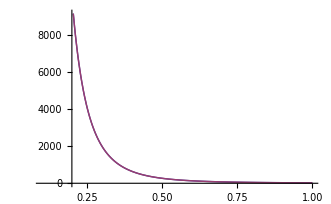

```mathematica
Plot[{(1+Csc[x/2]^4+Sec[x/2]^4),(((3+Cos[x]^2)^2)/((-1+Cos[x]^2)^2))},{x,0.1,Pi/21}]
```

Integrating in the solid angle

## Cross section

```mathematica
σ=Simplify[∫_0.1^1 (dcs/.Me->0)*(E1^2/α^2)*(2π)ⅆct]
```

Integrate::idiv: Integral of \!\(\((3 + ct\^2)\)\^2\/\((\(\(-1\)\) + ct\^2)\)\^2\) does not converge on \!\({0.1`, 1}\).

∫_0.1^1 ((3+ct^2)^2 π)/(2 (-1+ct^2)^2)ⅆct

This is the theoretical value (LAHIRI PAL book : eq 9.36)